```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]~StringJoin~".."]
```

H:\2_Projects\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

#### RandomMatrix

```mathematica
?RandomMatrix
```

```mathematica
m = RandomMatrix[3];
m//MatrixForm
```

(0.181616-0.249896 ⅈ | -0.204906+0.421527 ⅈ | 0.747858-2.36964 ⅈ
-2.17364+1.83383 ⅈ | -0.130083-0.532109 ⅈ | -1.46766-1.38237 ⅈ
-0.153702+0.0944883 ⅈ | 1.20034+1.04959 ⅈ | 0.182461-0.285982 ⅈ)

Check the distribution of arguments and phases of each entry

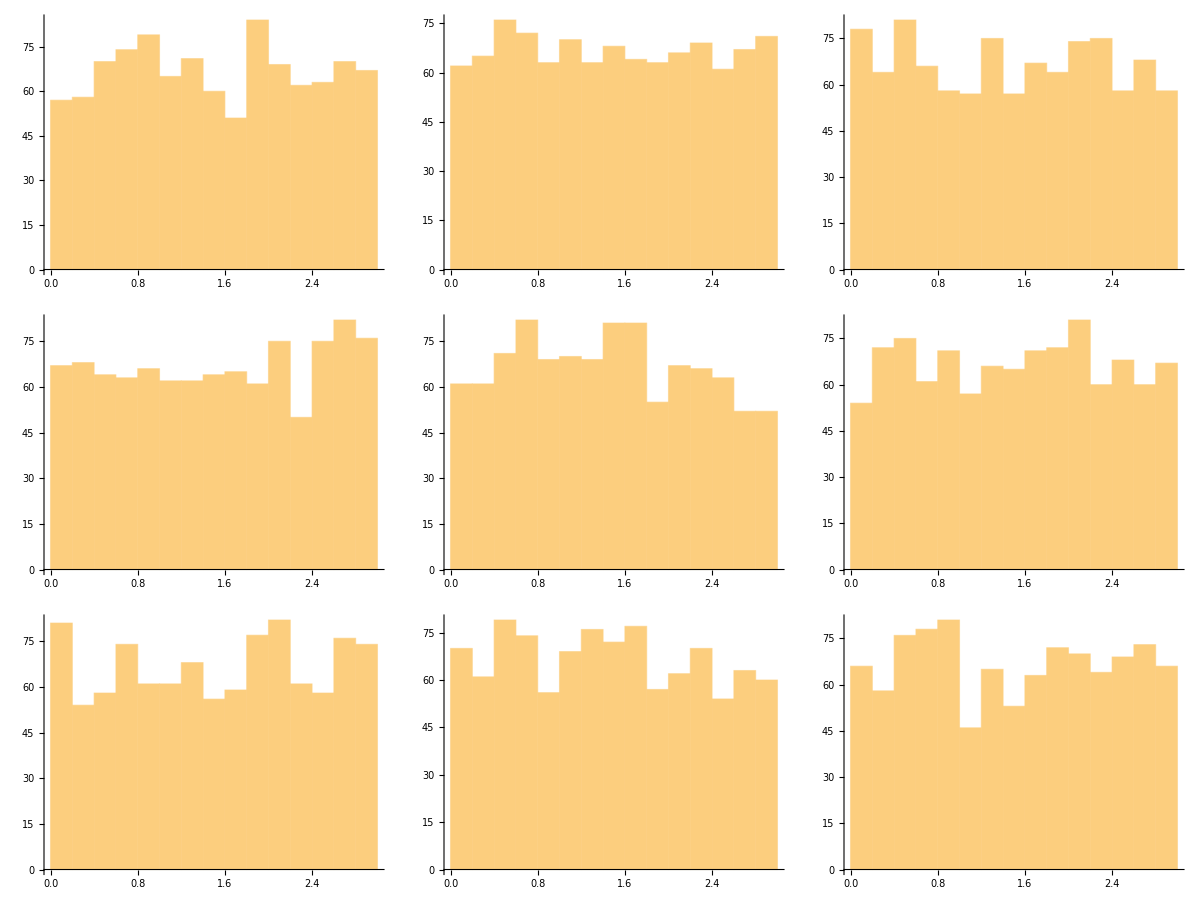
-Graphics-Histogram of the Norm of each element

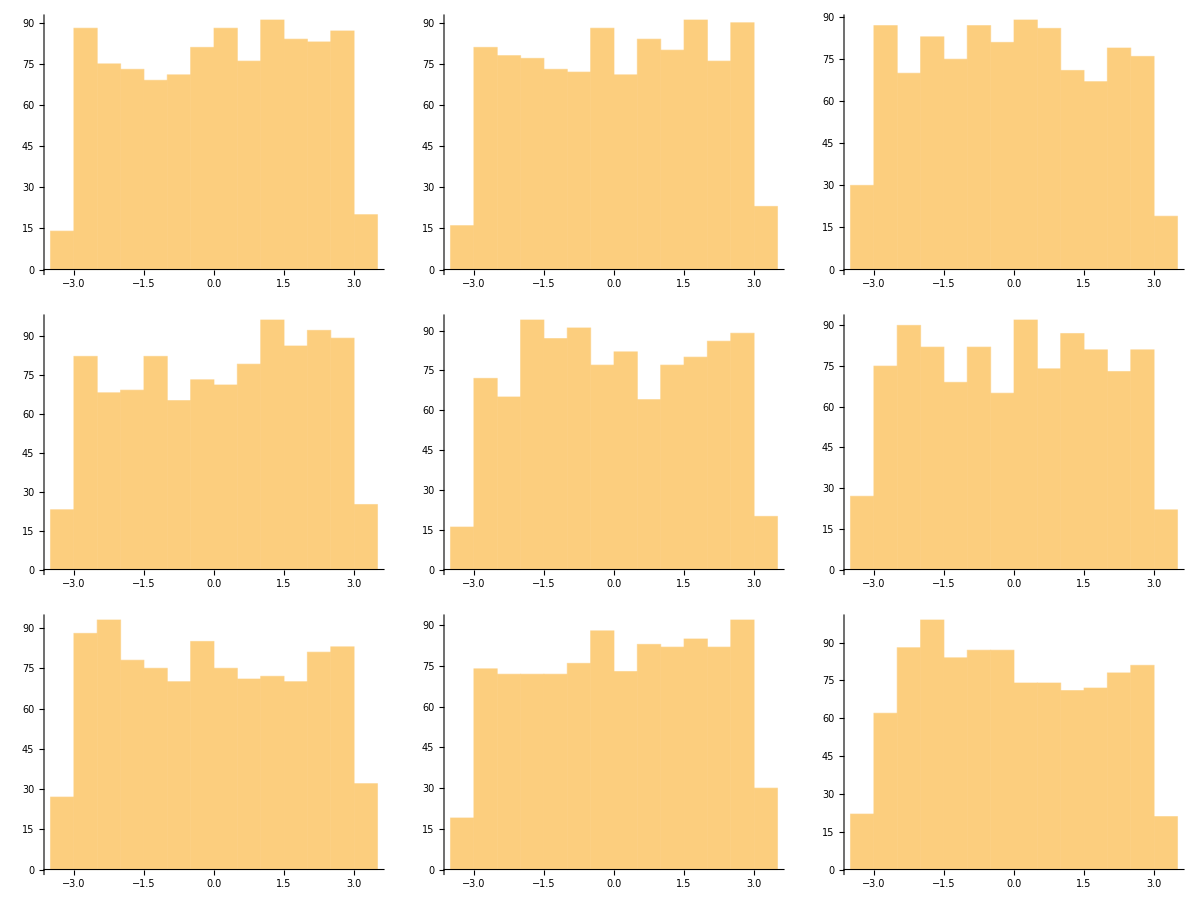
-Graphics-Histogram of the Phase of each element

```mathematica
n = 1000;
mlist = Table[RandomMatrix[3],{i,n}];
Labeled[
Grid[Table[Histogram[(Norm[#[[i,j]]]&)/@mlist],{i,1,3},{j,1,3}]],
"Histogram of the Norm of each element"
]
Labeled[
Grid[Table[Histogram[(Arg[#[[i,j]]]&)/@mlist],{i,1,3},{j,1,3}]],
"Histogram of the Phase of each element"
]
```

Note that this corresponds to NORMALLY DISTRIBUTED real and complex parts.

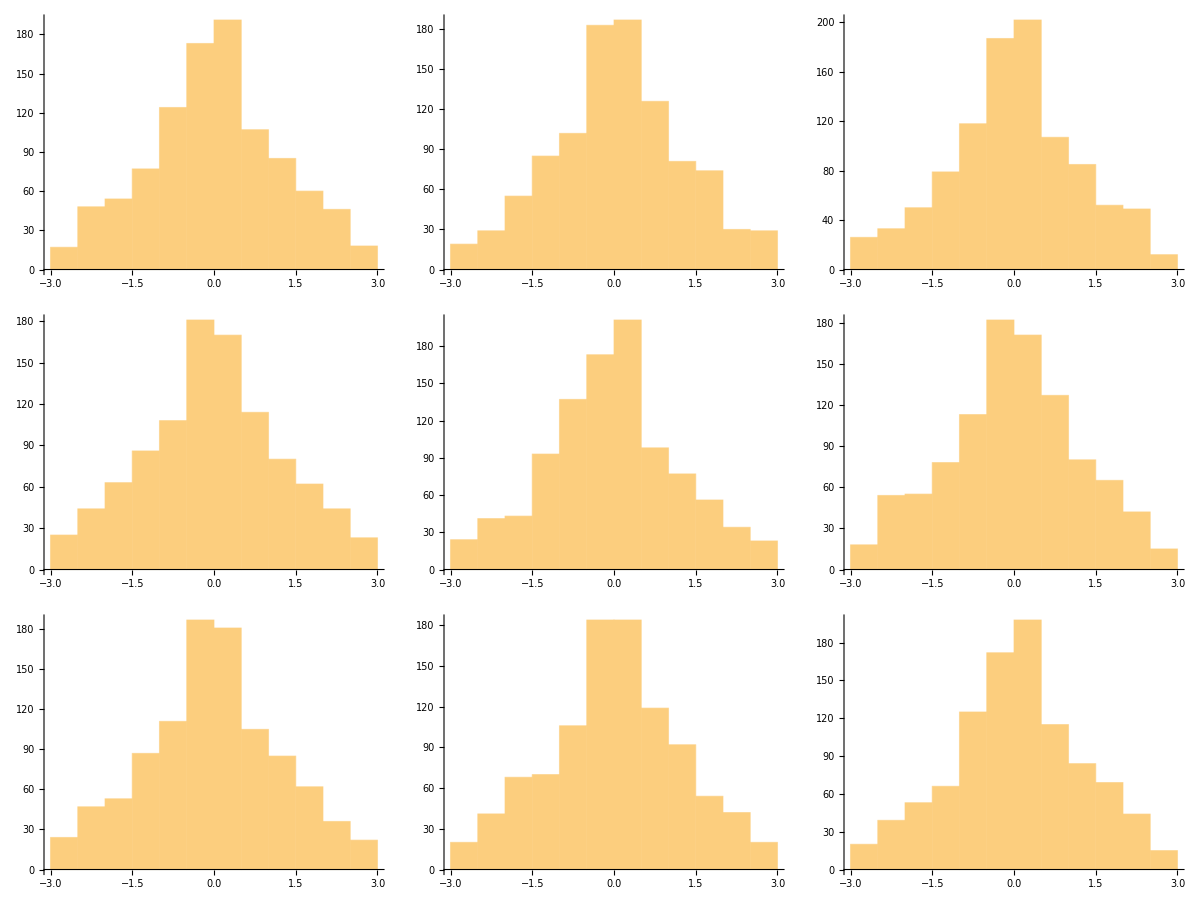
-Graphics-Histogram of the Real Parts of each element

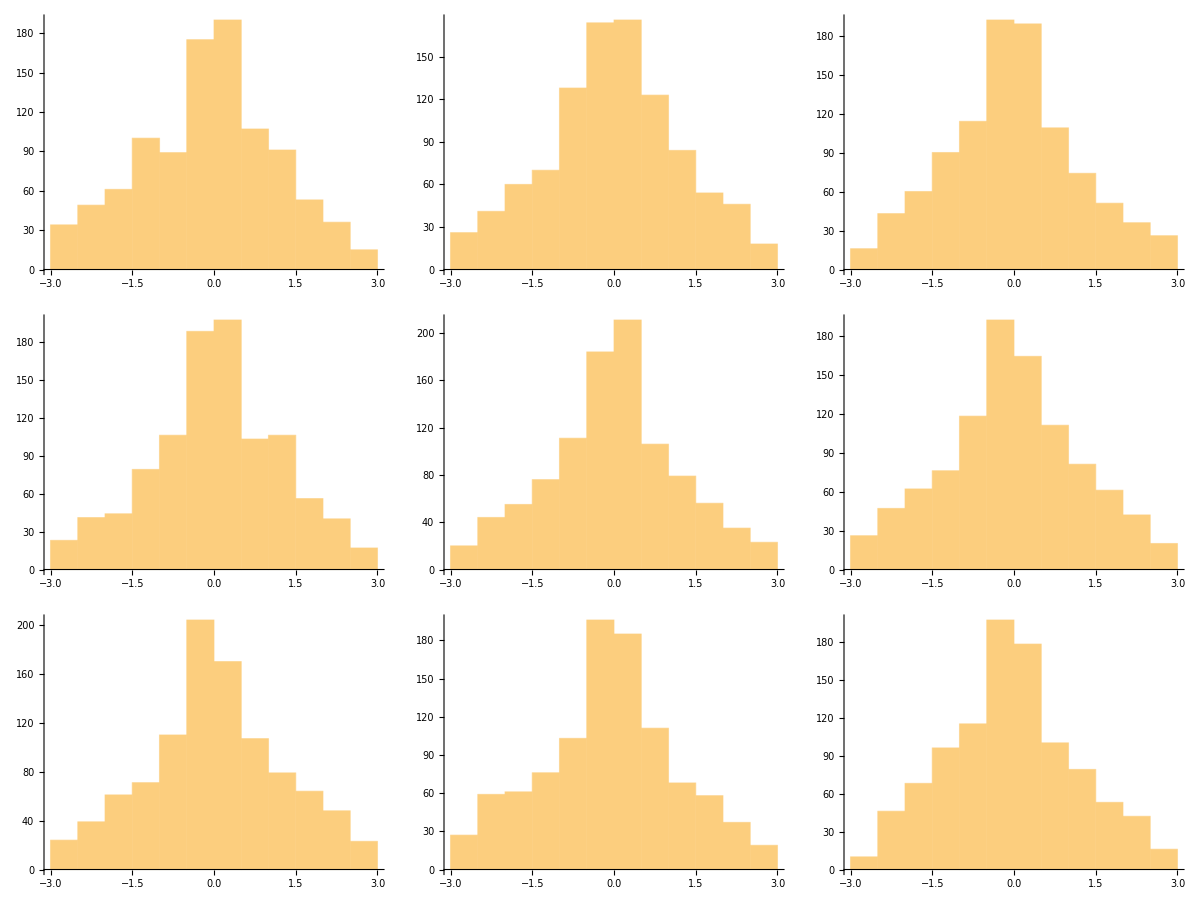
-Graphics-Histogram of the Imaginary Part of each element

```mathematica
n = 1000;
mlist = Table[RandomMatrix[3],{i,n}];
Labeled[
Grid[Table[Histogram[(Re[#[[i,j]]]&)/@mlist],{i,1,3},{j,1,3}]],
"Histogram of the Real Parts of each element"
]
Labeled[
Grid[Table[Histogram[(Im[#[[i,j]]]&)/@mlist],{i,1,3},{j,1,3}]],
"Histogram of the Imaginary Part of each element"
]
```

#### RandomUnitaryMatrix

```mathematica
?RandomUnitaryMatrix
```

RandomUnitaryMatrix generates random unitary matrices by perform QR decomposition on random matrices using RandomMatrix.

```mathematica
m = RandomUnitaryMatrix[3];
m//MatrixForm
```

(-0.00748768+0.668414 ⅈ | 0.202427+0.331092 ⅈ | 0.121345+0.622771 ⅈ
-0.0384817-0.358779 ⅈ | -0.535664+0.515652 ⅈ | 0.533213+0.180688 ⅈ
0.485323-0.432925 ⅈ | 0.294485+0.458091 ⅈ | -0.479573+0.224672 ⅈ)

```mathematica
UnitaryMatrixQ[m]
```

True

Check the distribution of arguments and phases of each entry

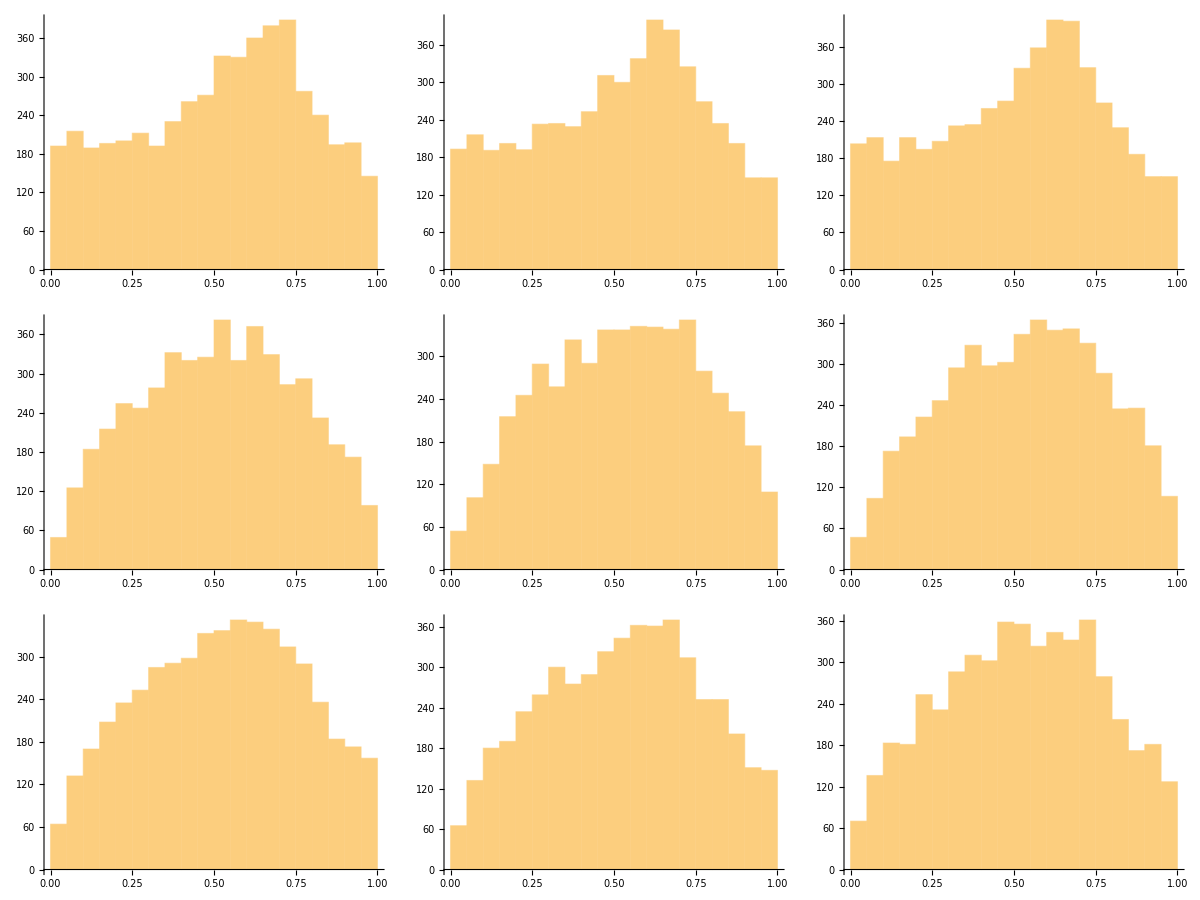
-Graphics-Histogram of the Norm of each element

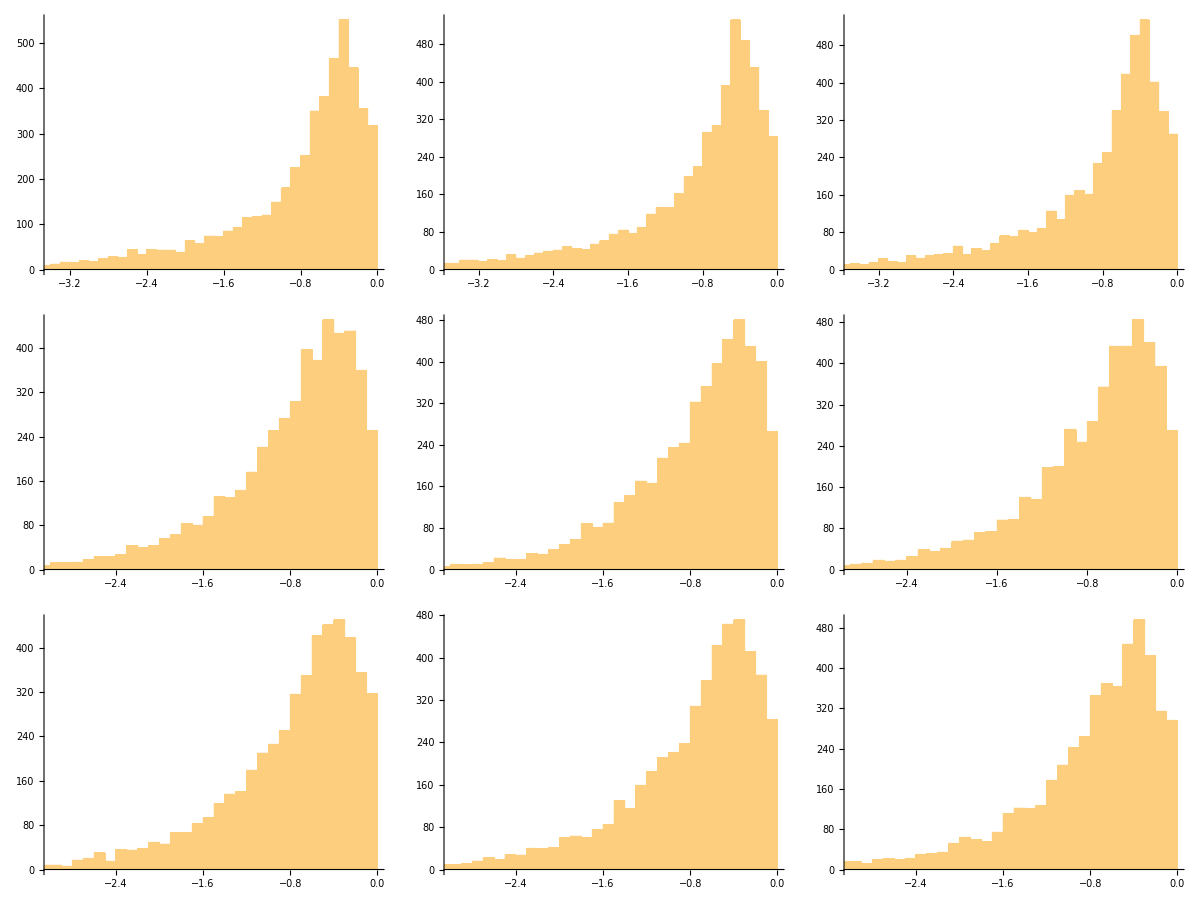
-Graphics-Histogram of Log of the Norm of each element

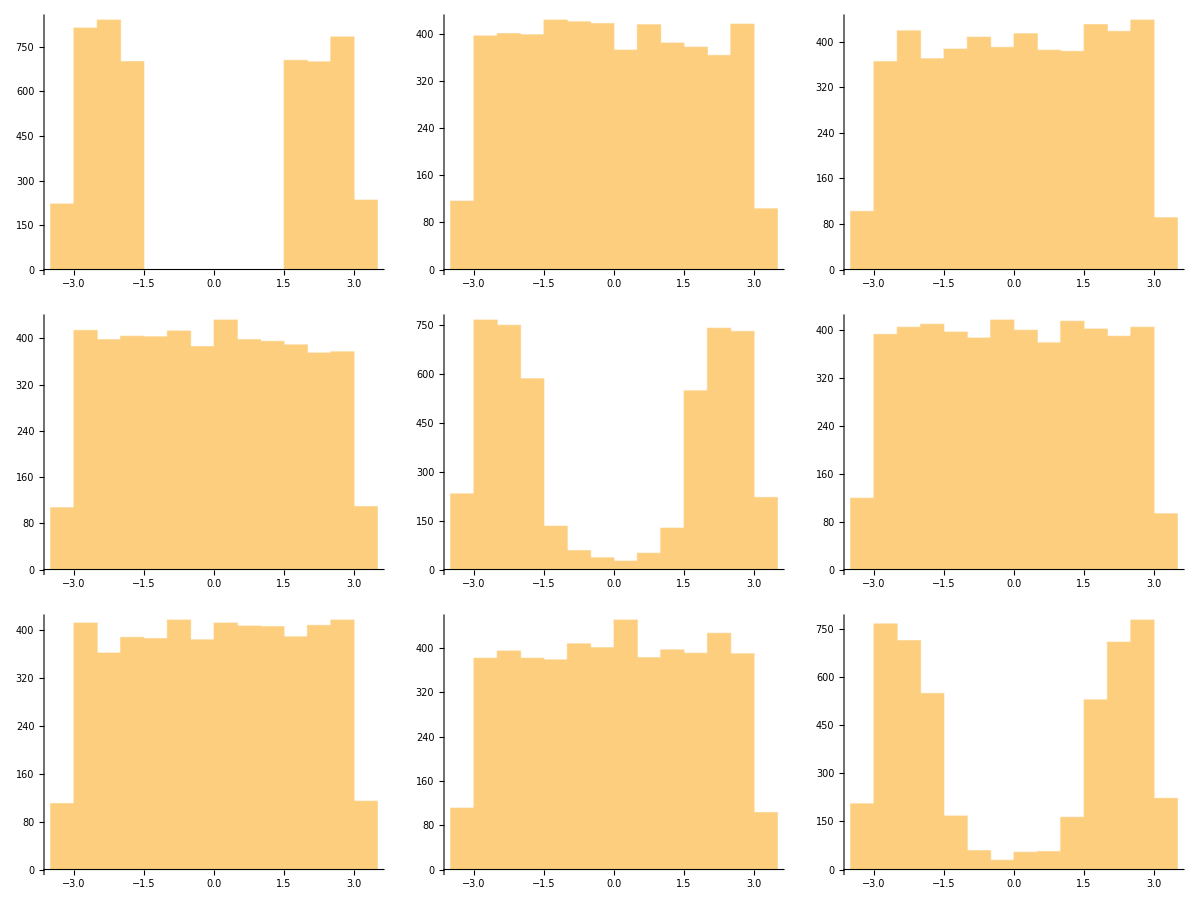
-Graphics-Histogram of the Phase of each element

```mathematica
n = 5000;
mlist = Table[RandomUnitaryMatrix[3],{i,n}];
Labeled[
Grid[Table[Histogram[(Norm[#[[i,j]]]&)/@mlist],{i,1,3},{j,1,3}]],
"Histogram of the Norm of each element"
]
Labeled[
Grid[Table[Histogram[(Log[Norm[#[[i,j]]]]&)/@mlist],{i,1,3},{j,1,3}]],
"Histogram of Log of the Norm of each element"
]
Labeled[
Grid[Table[Histogram[(Arg[#[[i,j]]]&)/@mlist],{i,1,3},{j,1,3}]],
"Histogram of the Phase of each element"
]
```

The norms approximately follow log normal distributions. The phases of the diagonal entries are almost normally distribute between 0 and π, while the phases of the off-diagonal entries are uniformly distributed.